# PDF OF THE WATER TABLE SOLVED NUMERICALLY

## Tutti e 3 metodi (no sale) con unione alla fine. Se ci sono modifiche vanno fatte prima nei singoli e poi riportate qui nella sezione associata!!

## CASE DWT/SWT/WL -NO SALT

### DATA

```mathematica
(*EXAMPLE (Tamea paper 2010)*)

(*n=0.463;
ψs=-11;
m=0.220;
sfcOLD=0.270/n;
sw=0.117/n;
ks=31;
λ0=0.30;
α=1.2;
Eatm=0.4;
b=20;
y0=-20;
kl=kl2=0.007;*)


	(*NP46 (Tamea paper 2010)*)

n=0.5;
ψs=-10;
m=0.20;
sfcOLD=0.270/n;
sw=0.117/n;
ks=10;
λ0=0.589;(* 1/day *)
α=0.95;(* cm *)
Eatm=0.48;(* cm/day *)
b=10;(* cm -mrd- *)
y0=0;(* cm *)
kl=0.001;
kl2=0.006;

	(*NP62 (Tamea paper 2010)*)

(*n=0.5;
ψs=-10;
m=0.20;
sfcOLD=0.270/n;
sw=0.117/n;
ks=10;
λ0=0.607;(* 1/day *)
α=0.97;(* cm *)
Eatm=0.46;(* cm/day *)
b=10;(* cm -mrd- *)
y0=-20;(* cm *)
kl=0.001;
kl2=0.003;*)
```

### FORMULATIONS

```mathematica
sfc=((0.05 Eatm)/ks)^(m/(2+3*m));
```

```mathematica
ψfc=ψs (1/sfc)^(1/m);
```

```mathematica
yCapill[v_,psi_,z_]:=z-ψs Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),-v/ks]+psi Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),-v/ks(psi/ψs)^(2+3m)];
```

```mathematica
vEq=1/(1+(0.39-0.73 *n)* b);
```

```mathematica
yc=yCapill[vEq,ψfc,0];
```

```mathematica
r[z_]=1/b Exp[z/b]
```

ⅇ^(z/10)/10

```mathematica
lim=ψfc-ψs-5b;
```

```mathematica
const=(ψfc-ψs-yc)/(ψfc-ψs-5b-yc);
```

```mathematica
h[y_]=If[y≥0,0,If[y≥yc,0,If[y<lim,y-ψfc+ψs,(y-yc)*(1-const^0.75)-(y-yc)^2 const/(ψfc-ψs-5b-yc)*(1-const^-0.25)]]];
```

```mathematica
dhdy[y_]=D[h[y],y];
```

```mathematica
β[y_]=If[y≥0,1,If[y≥yc,n(1- (1+(√-ψfc-√-ψs)/(√-ψs)y/yc)^(-2m)),If[y<lim,n(1-sfc),n (1-sfc)+n(1-dhdy[y])(-1+sfc-2 m sfc+2 m sfc √(sfc^(-1/m)))/((√-ψfc-√-ψs)/(√-ψs)(-1+2 m))]]];
```

```mathematica
Twtok[y_]=If[y≥yc,Eatm,Eatm Exp[h[y]/b]];
```

```mathematica
fl[y_]=If[y≥0,kl2(y0-y),kl (y0-y-ψs)];
```

```mathematica
b0=If[λ0*α<Eatm,α/(n(sfc-sw))Eatm/(Eatm-λ0 α),10^10];
```

```mathematica
sbar0=sfc-(Eatm (sfc-sw))/(Eatm+λ0 n (sfc-sw) b);
```

```mathematica
profile[sbar_]=-1/(1/b-n/α(sfc-sw))Log[(sbar-sw)/(sbar0-sw)]+b Log[(sfc-sbar)/(sfc-sbar0)]+(n(sfc-sw) b)/(α(1/b-n/α(sfc-sw)))Log[(1/b-n/α(sfc-sbar))/(1/b-n/α(sfc-sbar0))];
```

```mathematica
start=If[b>b0,sw+0.1^6,sfc-0.1^6];
```

```mathematica
sbarz[zz_?NumberQ]:=sb/.FindRoot[profile[sb]==zz,{sb,start,sbar0}];
```

```mathematica
λ[y_?NumberQ]:=Eatm/(n(sfc-sw)) (sbarz[h[y]]-sw)/(sfc-sbarz[h[y]])r[h[y]];
```

```mathematica
asint=(x/.FindRoot[-Twtok[x]+fl[x]==0,{x,y0}]);
```

### PDF EXPRESSION

```mathematica
esponente[y_?NumberQ]:=-NIntegrate[β[u]/α-(λ[u]* β[u])/(+Twtok[u]-fl[u]),{u,0,y}];
```

```mathematica
py[y_?NumberQ]:=β[y]/(+Twtok[y]-fl[y])*Exp[esponente[y]];
```

```mathematica
areay=NIntegrate[py[y],{y,asint,-0.00001},WorkingPrecision->16]+NIntegrate[py[y],{y,-0.00001,Infinity},WorkingPrecision->16];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-22.39663862951218}. NIntegrate obtained 7.465509833907003 and 0.0006755320099514806 for the integral and error estimates.

```mathematica
wt2y[wt_]=If[wt<ψs,wt+Abs[ψs],If[ψs≤wt<0,-0.000001,wt]];
```

## CASE SWT/WL - NO SALT

#### FORMULATIONS FOR SWT/WL

```mathematica
c0=0.35-0.65*n;
ylim1=y0-ψs-(Eatm/kl)  ;

β1[y_]:=Piecewise[{{1,y>=0},{n-n*(1+((sfc)^(-(1/(2m)))-1)*(y/yc1))^(-2m),y<0}}];  

vc=Eatm/(1+c0*b); 

yc1=ψs*sfc^(-1/m)*Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),-vc/ks sfc^(-(2+3 m)/m)]-ψs*Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),-vc/ks];
```

#### PDF EXPRESSION

```mathematica
(*is the same of the previous one but we consider only SWT/WL condiction*)
```

```mathematica
esponent2[y_?NumberQ]:=-NIntegrate[β1[u]/α-(λ0* β1[u])/(+Eatm-fl[u]),{u,0,y}];
py1[y_?NumberQ]:=β1[y]/(Eatm-fl[y])*Exp[esponent2[y]]
```

```mathematica
areay1=NIntegrate[py1[y],{y,ylim1,0}]+NIntegrate[py[y],{y,0,1000}] (*metti yc come limite inferiore*)
```

125.273

```mathematica
wt1y[wt1_]:=If[wt1<ψs,wt1+Abs[ψs],If[ψs≤wt1<0,-0.000001,wt1]];
```

## COMPARISON OF THE SOLUTIONS

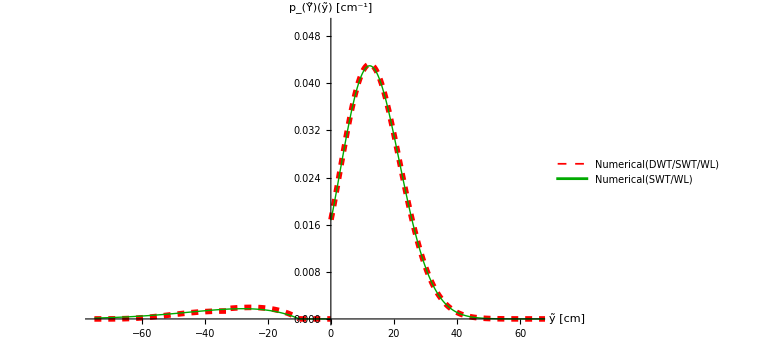

```mathematica
(*Struttura grafica standard da usare anche per il resto-> e per comaprare i grafici*)

(*range->(-75,65) e (0,+5 DEL PICCO) , NOME ""-> (-60, altezza picco)*)

NumericalNosalt=Plot[{py[wt2y[yi]]/areay ,py1[wt1y[yi]]/areay1},{yi,-75,75},PlotStyle->{{Red,Dashed,Thickness[0.007]},{Darker[Green],Thick} },PlotLegends->Placed[{" Numerical(DWT/SWT/WL)","Numerical(SWT/WL)"},{0.2,0.7}],(*Legenda in alto a destra*)
AxesLabel->{StyleForm["ỹ [cm]",FontSize->13],StyleForm["p_(Ỹ)(ỹ) [cm^-1]",FontSize->13]},(*Etichette degli assi*)
PlotRange->{{-75,65},{0,0.05}},(*Range degli assi*)
ImageSize->Large (*Dimensione del grafico*)]
```

```mathematica
NIntegrate[py[wt2y[yi]]/areay,{yi,-75,65}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in yi near {yi} = {-32.3448}. NIntegrate obtained 1. and 2.33906×10^-6 for the integral and error estimates.

1.

```mathematica
NIntegrate[py1[wt1y[yi]]/areay1,{yi,-75,65}]
```

0.998608

# ANALTYCAL SOLUTION SWT/WL - NO SALT

```mathematica
(*EXAMPLE-data*)

(*alpha=1.2; (*rainfall annual average depth [cm]*)
lambda=0.30; (*rainfall annual frequency [1/day]*)
ETMAX=0.4; (*potential evapotranspiration [cm/day]*)
m=0.22;  (*pore size index *)
ks=31; (*saturated hydraulic conductivity*)
n=0.463;(*porosity Best *)
psis=-11;(*saturared matric potential*)
y0=-20;(*exterrnal water body depth [cm]*)
kl=0.007;
kl2=0.007;
zr=20;(*Root zone depth[cm]*)
V=1; (*Vegetation coverage 1 = 100% *)
c0=0.35-0.65*n;*)


		(*NP46-data*)

alpha=0.95; (* rainfall annual average depth [cm]*)
lambda=0.589;(*rainfall annual frequency [1/day]*)
ETMAX=0.48; (* potential evapotranspiration [cm/day]*)
m=0.20; (* pore size index *)
ks=10; (*  saturated hydraulic conductivity*)
n=0.5; (* porosity Best *)
psis=-10;(* saturared matric potential*)
y0=0;(*exterrnal water body depth [cm]*)
zr=10; (*Root zone depth[cm]*)
V=1;(*Vegetation coverage 1 = 100% *)
c0=0.35-0.65*n; 
kl = 0.001;
kl2 = 0.006;


		(*NP62-data*)

(*alpha=0.97; (* rainfall annual average depth [cm]*)
lambda=0.607;(*rainfall annual frequency [1/day]*)
ETMAX=0.46; (* potential evapotranspiration [cm/day]*)
m=0.20; (* pore size index *)
ks=10; (*  saturated hydraulic conductivity*)
n=0.5; (* porosity Best *)
psis=-10;(* saturared matric potential*)
y0=-20;(*exterrnal water body depth [cm]*)
zr=10; (*Root zone depth[cm]*)
V=1;(*Vegetation coverage 1 = 100% *)
c0=0.35-0.65*n; 
kl = 0.001;
kl2 = 0.003;*)
```

```mathematica
(*VARIABLES NEEDED FOR PLOTS*)
sfc=((0.05*ETMAX)/ks)^(m/(2+3m));(*soil moisture at the field capacity*)
v=ETMAX/(1+c0*zr);(*capillary flux*)
yc=psis*sfc^(-1/m)*Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),-v/ks sfc^(-(2+3 m)/m)]-psis*Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),-v/ks](*critical depth*)
ylim=y0-psis-(ETMAX/kl)(*ylim-> depth at which evapotranspiration and lateral flows combine*)
```

-31.4938

-470.

```mathematica
(*PDF below ground - not normalised*)
Py[y_]:=1/(ETMAX+kl(y-y0+psis))ⅇ^(1/2 n (-(2 (y+(sfc^(1/(2 m)) yc)/((-1+2 m) (-1+sfc^(1/(2 m))))-((1+((-1+sfc^(-1/(2 m))) y)/yc)^(-2 m) (y-sfc^(1/(2 m)) y+sfc^(1/(2 m)) yc))/((-1+2 m) (-1+sfc^(1/(2 m))))))/alpha-(lambda (2 m Log[ETMAX+kl(-y0+psis)]+Hypergeometric2F1[2 m,2 m,1+2 m,((-1+sfc^(1/(2 m))) ETMAX-kl((-1+sfc^(1/(2 m))) y0-sfc^(1/(2 m)) yc-(-1+sfc^(1/(2 m))) psis))/((-1+sfc^(1/(2 m))) (ETMAX+kl(-y0+psis)))] (-(sfc^(1/(2 m)) yc kl)/((-1+sfc^(1/(2 m))) (ETMAX+kl(-y0+psis))))^(2 m)))/(m kl)-(lambda (-2 Log[ETMAX+kl(y-y0+psis)]-((1+((-1+sfc^(-1/(2 m))) y)/yc)^(-2 m) Hypergeometric2F1[2 m,2 m,1+2 m,((-1+sfc^(1/(2 m))) ETMAX-kl((-1+sfc^(1/(2 m))) y0-sfc^(1/(2 m)) yc-(-1+sfc^(1/(2 m))) psis))/((-1+sfc^(1/(2 m))) (ETMAX+kl(y-y0+psis)))] ((((-1+sfc^(1/(2 m))) y-sfc^(1/(2 m)) yc) kl)/((-1+sfc^(1/(2 m))) (ETMAX+kl(y-y0+psis))))^(2 m))/m))/kl)) (n-n (1+((-1+sfc^(-1/(2 m))) y)/yc)^(-2 m));
```

```mathematica
Pyn[ytilde_]=Re[Py[y]/.y->(ytilde-psis)];(*change of variable from y -> ytilde*)
```

```mathematica
I0=NIntegrate[Pyn[ytilde],{ytilde,ylim,0}]
```

6.06049

```mathematica
(*PROCEDIMENTO TAMEA 2010*)

Integral1=∫_0^ytilde (1/alpha-lambda/(ETMAX-kl2*(y0-ytilde)))ⅆytilde;
Integral2=FullSimplify[Integral1,Assumptions->{ytilde>=0,ETMAX>=0,kl>=0,lambda>=0}];
Pyab[ytilde_]:=1/(ETMAX-kl2*(y0-ytilde))*Exp[-Integral2]

I1=NIntegrate[Pyab[ytilde],{ytilde,0,1000}]
```

117.107

```mathematica
(*Final function for above and below ground (not normalised)*)
PFinal[ytilde_]:=Piecewise[{{Pyn[ytilde],ytilde<psis},{Pyab[ytilde],ytilde>0},{0,ytilde>psis <0}}]
```

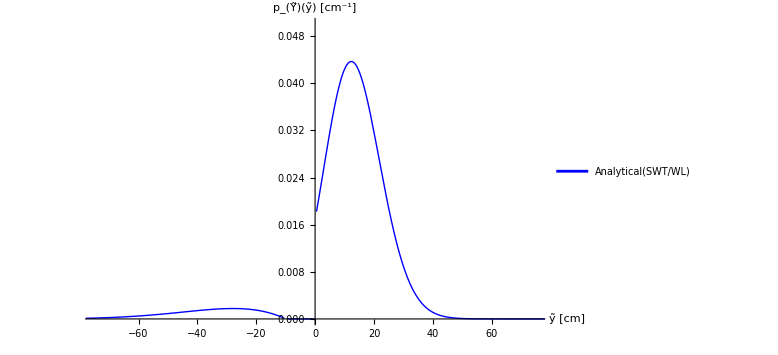

```mathematica
AnalyticalNOSALT=Plot[{PFinal[ytilde]/(I0+I1)},{ytilde,ylim,1000},
PlotStyle->{{Blue,Thick}},
PlotLegends->Placed[{"Analytical(SWT/WL)"},{0.17,0.6}],
AxesLabel->{StyleForm["ỹ [cm]",FontSize->13],StyleForm["p_(Ỹ)(ỹ) [cm^-1]",FontSize->13]},
PlotRange->{{-75,75},{0,0.05}},(*metti un valore che è 0.05 nell'ultima piu garnde del massimo*)
ImageSize->Large (*Dimensione del grafico*)
]
```

```mathematica
NIntegrate[PFinal[ytilde]/(I0+I1),{ytilde,ylim,1000}]
```

1.01709

# NUMERICAL SOLUTION TRAJECTORIES SWT/WL - NO SALT

#### DATA EVERGLADES STATIONS

```mathematica
(*EXAMPLE*)

alpha=1.2; (* rainfall annual average depth [cm]*)
lambda0=0.3;(*rainfall annual frequency [1/day]*)
ETMAX=0.4; (* potential evapotranspiration [cm/day]*)
m=0.22; (* pore size index *)
ks=31; (*  saturated hydraulic conductivity*)
n=0.463; (* porosity Best *)
psis=-11;(* saturared matric potential*)
y0=-20;(*exterrnal water body depth [cm]*)
ymin=-75;(* minimum observed water depth*)
zr=20; (*Root zone depth[cm]*)
V=1;(*Vegetation coverage 1 = 100% *)
c0=0.35-0.65*n; 
kl1 = 0.007;
kl2 = 0.007;


(*EVERGLADES NP46*)

(*alpha=0.95; (* rainfall annual average depth [cm]*)
lambda0=0.589;(*rainfall annual frequency [1/day]*)
ETMAX=0.48; (* potential evapotranspiration [cm/day]*)
m=0.20; (* pore size index *)
ks=10; (*  saturated hydraulic conductivit*)
n=0.5; (* porosity Best *)
psis=-10;(* saturared matric potential*)
y0=0;(*exterrnal water body depth [cm]*)
ymin=-75;(* minimum observed water depth*)
zr=10; (*Root zone depth[cm]*)
V=1;(*Vegetation coverage 1 = 100% *)
c0=0.35-0.65*n; 
kl1 = 0.001;
kl2 = 0.006;*)

(*EVERGLADES NP62*)

(*alpha=0.97; (* rainfall annual average depth [cm]*)
lambda0=0.607;(*rainfall annual frequency [1/day]*)
ETMAX=0.46; (* potential evapotranspiration [cm/day]*)
m=0.20; (* pore size index *)
ks=10; (*  saturated hydraulic conductivit*)
n=0.5; (* porosity Best *)
psis=-10;(* saturared matric potential*)
y0=-20;(*exterrnal water body depth [cm]*)
ymin=-75;(* minimum observed water depth*)
zr=10; (*Root zone depth[cm]*)
V=1;(*Vegetation coverage 1 = 100% *)
c0=0.35-0.65*n; 
kl1 = 0.001;
kl2 = 0.003;*)
```

### PRELIMINARY EQUATIONS

```mathematica
sfc=((0.05*ETMAX)/ks)^(m/(2+3m));(*soil moisture at field capacity*)
v=ETMAX/(1+c0*zr);(*capillary flux not dipendent from z*)
yc=psis*sfc^(-1/m)*Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),-v/ks sfc^(-(2+3 m)/m)]-psis*Hypergeometric2F1[1/(2+3m),1,1+1/(2+3m),-v/ks] ;(*critical depth*)
fc[y_] := Piecewise[{{kl2*(y0-y),y>=0},{kl1*(y0-y-psis),y < 0}}]; (*Lateral Flow*)

(*Specific yield*)

βc[y_]:=Piecewise[{{1,y>=0},{n-n*(1+((sfc)^(-(1/(2m)))-1)*(y/yc))^(-2m),y<0}}];  (*TAMEA FORMULATION*)
```

#### DATA FOR MONTECARO SIMULATION

```mathematica
RandomExp[alpha_]:=RandomVariate[ExponentialDistribution[1/alpha]]; (*function for random value of alpha*)
tmax=365;(*maximun time of the analysis*)
tDay=360; (*definition of a certain day to find PDF(y)*)
dt=1; (*increment of time-> in this case every day*)
totTrajectory=500;(*number of trajectories decided*)
Trajectory=0; (*first Trajectory*)
TrajectoryA=2; (*trajectory chosen to analyse the trend in βc,fc,recharge and water table values*)

p={};(* list with the value of y and t for all the Trajectorys*)
yDay={} ; (*list to collect values of y in that day for all the Trajectorys *)
WatertableList={};(*list with the value of y and t for Trajectory A*)
BetaList1={};(*list with the value of beta and t for Trajectory A*)
LateralflowList={};(*list with the value of fc and t for Trajectory A*)
RechargeList={};(*list with the value of recharge and t for Trajectory A*)
```

#### MONTECARLO SIMULATION - EULERO METHOD

```mathematica
While[Trajectory<totTrajectory,

yt={{0,ymin}}; (*list to collect values of (time,y) for one trajectory.I impose to start from ymin*)
yi= ymin; (*first value of y=ymin*)

For[t=0,t<=tmax,t+=dt,
recharge=If[Random[]>dt*lambda0,0,RandomExp[alpha]]; (*randomly pick a value of rain depth from the distribution*)
yi1=yi+dt*(recharge-ETMAX+fc[yi])/Re[βc[yi]];  (*Eulero method*)
AppendTo[yt,{t,yi1}];(*Add y value to its list*)

yi=yi1; (*pass yi to next *)	

If[Trajectory==TrajectoryA,(*If the trajectory is trajectory A then fill in the lists for beta,fc,recharge and water table*)
AppendTo[WatertableList,{t,yi}];
AppendTo[BetaList1,{t,Re[βc[yi]]}];
AppendTo[LateralflowList,{t,fc[yi]}];
AppendTo[RechargeList,{t,recharge}];];
]; 

AppendTo[p,yt];  (*Add the graph of the i-Trajectory to p*)
valueday=SelectFirst[yt,#[[1]]==tDay&]; (*select from yt the couple of value when time=tDay*)
AppendTo[yDay,valueday[[2]]]; (*adding the value of y associated to tDay at the list yDay*)
	Trajectory++;
];
```

```mathematica
GraphicB=Histogram[yDay,{5},"PDF",ChartStyle->{Directive[RGBColor[1,0.6,0],Opacity[0.5]]},AxesOrigin->{0,0},ImageSize->Large];
```

### IMPORT DATA FROM NP46

```mathematica
datiNP46=Import["C:\Users\della\Desktop\Final script\DATA STATION NP46 NP62\Data_NP46.csv"];
PointNP46=ListPlot[datiNP46,PlotStyle->{Gray,PointSize[Medium]},PlotRange->{{-75,75},{0,0.05}},PlotMarkers->{"●",12},PlotLegends->Placed[{"In situ data"},{0.12,0.52}]];
```

### Creazione di un grafico vuoto -> per avere diciamo la struttura del grafico di partenza (plotrange, nome assi, nome stazione )

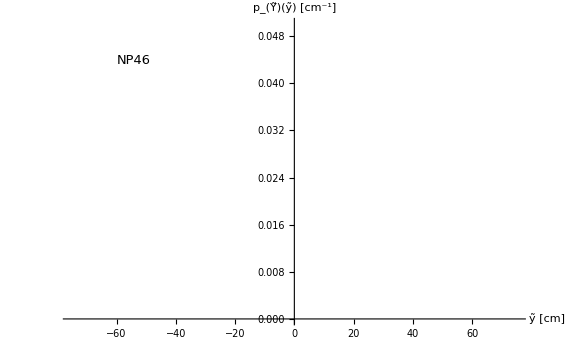

```mathematica
StrutturaPlot=Plot[{},{yi,-75,75},
AxesLabel->{StyleForm["ỹ [cm]",FontSize->13],StyleForm["p_(Ỹ)(ỹ) [cm^-1]",FontSize->13]},(*Etichette degli assi*)
Epilog->{Inset[Style["NP46",13],{-60,0.045},{Left,Top}]},
PlotRange->{{-75,75},{0,0.05}},(*Range degli assi*)
ImageSize->Large (*Dimensione del grafico*)]
```

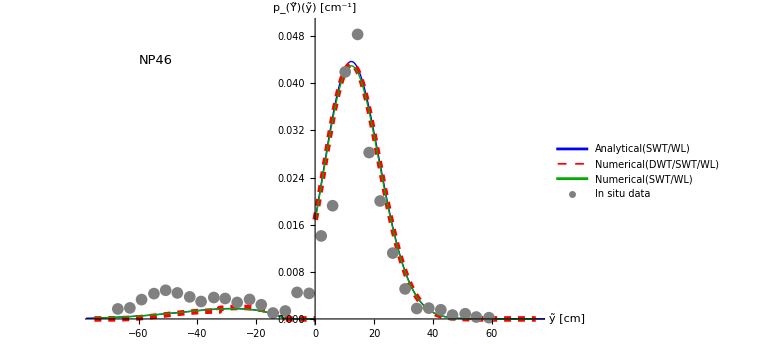

```mathematica
(*qui scegli i grafici da sovrapporre-> strutturaplot sempre davanti-> modifica ordine altri o togli cio che nn vuoi*)
Show[StrutturaPlot,(*GraphicB,*)AnalyticalNOSALT,NumericalNosalt,PointNP46]
```